# Rayleigh Quotient and Inverse Iteration

For the next few lectures A∈ℝ^(m×m) is symmetric A=Aᵀ.  This means that A is orthogonally diagonalizable with real eigenvalues i.e.
	A=Q.Λ.Qᵀ
with Q=(q_1 | | | q_2 | | | … | | | q_m) satisfying A.q_i=λ_i q_i with Λ=dia(λ_1,λ_2,…,λ_m).

## Rayleigh Quotient

Critical points v of the Rayleigh quotient
	r(x)=(x.A.x)/(x.x)
are eigenvectors of A with eigenvalues r(v).   This is immediate once you differentiate r(x)
	∇r(x).b=((b.A.x + x.A.b) (x.x)-(x.A.x)(x.b + b.x))/(x.x)^2=(2(x.A.b) (x.x) - 2(x.A.x)(x.b))/(x.x)^2
which gives
	∇r(x)=2 (x.x)^-2(A.x-r(x) x).
We can look at this in a projected contour plot in any dimension.

```mathematica
m=6; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_,x_]:= x.A.x/(x.x)
V=Eigenvectors[A];
{u1,u2}=Map[Normalize,RandomReal[{-1,1},{2,m}]];
TabView[
Table[ContourPlot[r[A,V⟦i⟧+ϵ1 u1 +ϵ2 u2],{ϵ1,-0.5,0.5},{ϵ2,-0.5,0.5},
Contours->54,PlotPoints->50,Epilog->{Red,Point[{0,0}]}],
{i,m}]]
```

123456

```mathematica
r[A_List,x_List]:= x.A.x/(x.x)
m=3; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
λs=Eigenvalues[A];
{λMin,λMax}={Min[λs],Max[λs]};
```

```mathematica
ParametricPlot
```

ParametricPlot

```mathematica
PolyhedronData[Sphere[{0,0,0},1]]
```

PolyhedronData::notdef: PolyhedronData has no value associated with the specified argument(s).

PolyhedronData[Sphere[{0,0,0},1]]

```mathematica
FullForm[Graphics3D[Sphere[{0,0,0},1]]]
```

Graphics3D[Sphere[List[0,0,0],1]]

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
V=Eigenvectors[A];
Pic=ParametricPlot3D[{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},{θ,0,2Pi},{ϕ,0, π},
ColorFunction->Function[{x,y,z,θ,ϕ},Hue[{x,y,z}.A.{x,y,z}]],PlotPoints->50];
TabView[{
Show[Pic,ViewPoint->3V⟦1⟧],
Show[Pic,ViewPoint->3V⟦2⟧],
Show[Pic,ViewPoint->3V⟦3⟧]}]
```

123

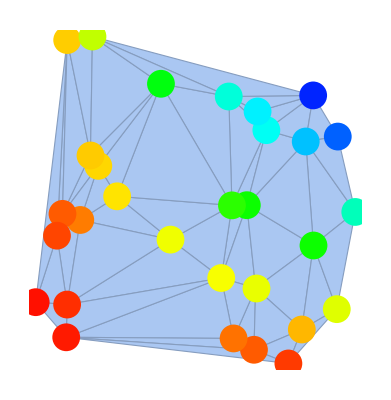
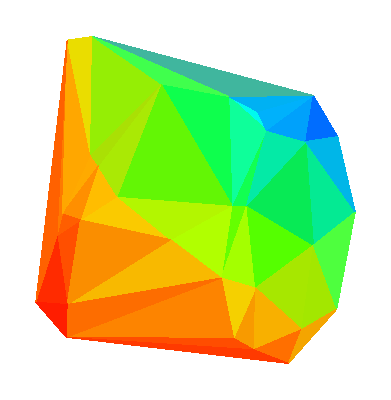

```mathematica
p=RandomReal[{0,1},{30,2}];
c=Map[Hue[Sin[#⟦1⟧ #⟦2⟧]]&,p];
R=DelaunayMesh[p];
{Show[DelaunayMesh[p],Graphics[Graphics[MapThread[{PointSize[.05],#1,Point[#2]}&,{c,p}]]]],
Graphics[GraphicsComplex[MeshCoordinates[R],MeshCells[R,2],VertexColors->c]]}
```

```mathematica
r[A_List,x_List]:= x.A.x/(x.x)
m=3; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
{λs,V}=Eigensystem[A];
{λMin,λMax}={Min[λs],Max[λs]};
MyMesh =DiscretizeRegion[Sphere[{0,0,0},1]];
{pts,cells}={MeshCoordinates[MyMesh],MeshCells[MyMesh,2]};
colors =Map[Hue[0.9(#.A.#-λMin)/(λMax-λMin)]&,pts];
Pic=Graphics3D[{{PointSize[0.02],Point[V]},GraphicsComplex[pts,cells,VertexColors->colors]}];
TabView[{
1->Show[Pic, ViewPoint->2 V⟦1⟧],
2->Show[Pic, ViewPoint->2 V⟦2⟧],
3->Show[Pic, ViewPoint->2 V⟦3⟧],
-1->Show[Pic, ViewPoint->-2 V⟦1⟧],
-2->Show[Pic, ViewPoint->-2 V⟦2⟧],
-3->Show[Pic, ViewPoint->-2 V⟦3⟧]
}]
```

123456

```mathematica
MeshCoordinates[DiscretizeRegion[Sphere[{0,0,0},1]]]
```

{{-0.607062,0.,0.794654},{0.894427,0.,0.447214},{0.,0.,1.},{-0.723607,-0.525731,0.447214},{-0.723607,0.525731,0.447214},{0.,0.,-1.},{0.276393,-0.850651,0.447214},{0.276393,0.850651,0.447214},{-0.187592,-0.57735,0.794654},{-0.187592,0.57735,0.794654},{0.491123,0.356822,0.794654},{0.491123,-0.356822,0.794654},{0.607062,0.,-0.794654},{0.187592,-0.57735,-0.794654},{0.187592,0.57735,-0.794654},{-0.491123,0.356822,-0.794654},{-0.491123,-0.356822,-0.794654},{0.794654,-0.57735,0.187592},{-0.303531,-0.934172,0.187592},{0.794654,0.57735,0.187592},{-0.303531,0.934172,0.187592},{-0.982247,0.,0.187592},{0.982247,0.,-0.187592},{0.303531,-0.934172,-0.187592},{0.303531,0.934172,-0.187592},{-0.794654,-0.57735,-0.187592},{-0.794654,0.57735,-0.187592},{0.723607,-0.525731,-0.447214},{-0.894427,0.,-0.447214},{0.723607,0.525731,-0.447214},{-0.276393,-0.850651,-0.447214},{-0.276393,0.850651,-0.447214},{-0.213042,-0.947677,0.237743},{-0.115625,-0.950755,0.287569},{-0.0143242,-0.942084,0.33507},{0.0871575,-0.92155,0.378351},{0.185096,-0.890336,0.415981},{0.204995,-0.829094,0.520174},{0.127698,-0.796779,0.590623},{0.0468717,-0.753743,0.655496},{-0.0345446,-0.701214,0.712114},{-0.113547,-0.641464,0.758704},{-0.214646,-0.660613,0.719387},{-0.240241,-0.739387,0.62896},{-0.262866,-0.809017,0.525731},{-0.28128,-0.865689,0.414082},{-0.294826,-0.907382,0.299558},{0.185096,0.890336,0.415981},{0.0871575,0.92155,0.378351},{-0.0143242,0.942084,0.33507},{-0.115625,0.950755,0.287569},{-0.213042,0.947677,0.237743},{-0.294826,0.907382,0.299558},{-0.28128,0.865689,0.414082},{-0.262866,0.809017,0.525731},{-0.240241,0.739387,0.62896},{-0.214646,0.660613,0.719387},{-0.113547,0.641464,0.758704},{-0.0345446,0.701214,0.712114},{0.0468717,0.753743,0.655496},{0.127698,0.796779,0.590623},{0.204995,0.829094,0.520174},{0.213042,-0.947677,-0.237743},{0.115625,-0.950755,-0.287569},{0.0143242,-0.942084,-0.33507},{-0.0871575,-0.92155,-0.378351},{-0.185096,-0.890336,-0.415981},{-0.204995,-0.829094,-0.520174},{-0.127698,-0.796779,-0.590623},{-0.0468717,-0.753743,-0.655496},{0.0345446,-0.701214,-0.712114},{0.113547,-0.641464,-0.758704},{0.214646,-0.660613,-0.719387},{0.240241,-0.739387,-0.62896},{0.262866,-0.809017,-0.525731},{0.28128,-0.865689,-0.414082},{0.294826,-0.907382,-0.299558},{-0.185096,0.890336,-0.415981},{-0.0871575,0.92155,-0.378351},{0.0143242,0.942084,-0.33507},{0.115625,0.950755,-0.287569},{0.213042,0.947677,-0.237743},{0.294826,0.907382,-0.299558},{0.28128,0.865689,-0.414082},{0.262866,0.809017,-0.525731},{0.240241,0.739387,-0.62896},{0.214646,0.660613,-0.719387},{0.113547,0.641464,-0.758704},{0.0345446,0.701214,-0.712114},{-0.0468717,0.753743,-0.655496},{-0.127698,0.796779,-0.590623},{-0.204995,0.829094,-0.520174},{-0.421466,-0.306213,-0.85358},{-0.343464,-0.249541,-0.905407},{-0.25923,-0.188342,-0.947274},{-0.171732,-0.12477,-0.977211},{-0.0842933,-0.0612426,-0.994557},{0.0321972,-0.0990927,-0.994557},{0.0655957,-0.201883,-0.977211},{0.0990171,-0.304743,-0.947274},{0.131191,-0.403766,-0.905407},{0.160986,-0.495463,-0.85358},{0.0772556,-0.560793,-0.824344},{-0.0410381,-0.535025,-0.843839},{-0.16246,-0.5,-0.850651},{-0.28128,-0.456966,-0.843839},{-0.392127,-0.408281,-0.824344},{0.209914,-0.969074,-0.129734},{0.107439,-0.991992,-0.0664011},{0.,-1.,-2.97114×10^-17},{-0.107439,-0.991992,0.0664011},{-0.209914,-0.969074,0.129734},{-0.307919,-0.947677,0.084229},{-0.308919,-0.950755,-0.0251864},{-0.306102,-0.942084,-0.137036},{-0.29943,-0.92155,-0.24716},{-0.289288,-0.890336,-0.351587},{0.160986,0.495463,-0.85358},{0.131191,0.403766,-0.905407},{0.0990171,0.304743,-0.947274},{0.0655957,0.201883,-0.977211},{0.0321972,0.0990927,-0.994557},{-0.0842933,0.0612426,-0.994557},{-0.171732,0.12477,-0.977211},{-0.25923,0.188342,-0.947274},{-0.343464,0.249541,-0.905407},{-0.421466,0.306213,-0.85358},{-0.392127,0.408281,-0.824344},{-0.28128,0.456966,-0.843839},{-0.16246,0.5,-0.850651},{-0.0410381,0.535025,-0.843839},{0.0772556,0.560793,-0.824344},{-0.289288,0.890336,-0.351587},{-0.29943,0.92155,-0.24716},{-0.306102,0.942084,-0.137036},{-0.308919,0.950755,-0.0251864},{-0.307919,0.947677,0.084229},{-0.209914,0.969074,0.129734},{-0.107439,0.991992,0.0664011},{0.,1.,2.97114×10^-17},{0.107439,0.991992,-0.0664011},{0.209914,0.969074,-0.129734},{-0.0321972,-0.0990927,0.994557},{-0.0655957,-0.201883,0.977211},{-0.0990171,-0.304743,0.947274},{-0.131191,-0.403766,0.905407},{-0.160986,-0.495463,0.85358},{-0.0772556,-0.560793,0.824344},{0.0410381,-0.535025,0.843839},{0.16246,-0.5,0.850651},{0.28128,-0.456966,0.843839},{0.392127,-0.408281,0.824344},{0.421466,-0.306213,0.85358},{0.343464,-0.249541,0.905407},{0.25923,-0.188342,0.947274},{0.171732,-0.12477,0.977211},{0.0842933,-0.0612426,0.994557},{0.307919,-0.947677,-0.084229},{0.308919,-0.950755,0.0251864},{0.306102,-0.942084,0.137036},{0.29943,-0.92155,0.24716},{0.289288,-0.890336,0.351587},{-0.160986,0.495463,0.85358},{-0.131191,0.403766,0.905407},{-0.0990171,0.304743,0.947274},{-0.0655957,0.201883,0.977211},{-0.0321972,0.0990927,0.994557},{0.0842933,0.0612426,0.994557},{0.171732,0.12477,0.977211},{0.25923,0.188342,0.947274},{0.343464,0.249541,0.905407},{0.421466,0.306213,0.85358},{0.392127,0.408281,0.824344},{0.28128,0.456966,0.843839},{0.16246,0.5,0.850651},{0.0410381,0.535025,0.843839},{-0.0772556,0.560793,0.824344},{0.289288,0.890336,0.351587},{0.29943,0.92155,0.24716},{0.306102,0.942084,0.137036},{0.308919,0.950755,0.0251864},{0.307919,0.947677,-0.084229},{0.104192,0.,-0.994557},{0.212272,0.,-0.977211},{0.320426,0.,-0.947274},{0.424544,0.,-0.905407},{0.520961,0.,-0.85358},{0.557219,-0.0998201,-0.824344},{0.496158,-0.204362,-0.843839},{0.425325,-0.309017,-0.850651},{0.347681,-0.408723,-0.843839},{0.267125,-0.499101,-0.824344},{0.267125,0.499101,-0.824344},{0.347681,0.408723,-0.843839},{0.425325,0.309017,-0.850651},{0.496158,0.204362,-0.843839},{0.557219,0.0998201,-0.824344},{0.729385,-0.641464,0.237743},{0.652383,-0.701214,0.287569},{0.565332,-0.753743,0.33507},{0.471161,-0.796779,0.378351},{0.373581,-0.829094,0.415981},{0.399783,-0.907382,-0.129734},{0.496158,-0.865689,-0.0664011},{0.587785,-0.809017,-2.97114×10^-17},{0.669998,-0.739387,0.0664011},{0.739432,-0.660613,0.129734},{0.373581,0.829094,0.415981},{0.471161,0.796779,0.378351},{0.565332,0.753743,0.33507},{0.652383,0.701214,0.287569},{0.729385,0.641464,0.237743},{0.739432,0.660613,0.129734},{0.669998,0.739387,0.0664011},{0.587785,0.809017,2.97114×10^-17},{0.496158,0.865689,-0.0664011},{0.399783,0.907382,-0.129734},{-0.967128,-0.0902331,0.237743},{-0.939952,-0.183833,0.287569},{-0.900402,-0.277497,0.33507},{-0.849513,-0.367666,0.378351},{-0.789563,-0.451166,0.415981},{-0.725168,-0.451166,0.520174},{-0.718321,-0.367666,0.590623},{-0.702368,-0.277497,0.655496},{-0.677569,-0.183833,0.712114},{-0.645156,-0.0902331,0.758704},{-0.69461,0.,0.719387},{-0.777438,0.,0.62896},{-0.850651,0.,0.525731},{-0.91024,0.,0.414082},{-0.954078,0.,0.299558},{-0.789563,0.451166,0.415981},{-0.849513,0.367666,0.378351},{-0.900402,0.277497,0.33507},{-0.939952,0.183833,0.287569},{-0.967128,0.0902331,0.237743},{-0.645156,0.0902331,0.758704},{-0.677569,0.183833,0.712114},{-0.702368,0.277497,0.655496},{-0.718321,0.367666,0.590623},{-0.725168,0.451166,0.520174},{-0.653173,-0.550258,0.520174},{-0.571645,-0.569549,0.590623},{-0.480959,-0.58224,0.655496},{-0.384216,-0.587599,0.712114},{-0.285181,-0.585697,0.758704},{-0.267125,-0.499101,0.824344},{-0.347681,-0.408723,0.843839},{-0.425325,-0.309017,0.850651},{-0.496158,-0.204362,0.843839},{-0.557219,-0.0998201,0.824344},{-0.557219,0.0998201,0.824344},{-0.496158,0.204362,0.843839},{-0.425325,0.309017,0.850651},{-0.347681,0.408723,0.843839},{-0.267125,0.499101,0.824344},{-0.285181,0.585697,0.758704},{-0.384216,0.587599,0.712114},{-0.480959,0.58224,0.655496},{-0.571645,0.569549,0.590623},{-0.653173,0.550258,0.520174},{-0.373581,-0.829094,-0.415981},{-0.471161,-0.796779,-0.378351},{-0.565332,-0.753743,-0.33507},{-0.652383,-0.701214,-0.287569},{-0.729385,-0.641464,-0.237743},{-0.771865,-0.560793,-0.299558},{-0.736399,-0.535025,-0.414082},{-0.688191,-0.5,-0.525731},{-0.62896,-0.456966,-0.62896},{-0.561951,-0.408281,-0.719387},{-0.468905,-0.452213,-0.758704},{-0.44011,-0.546989,-0.712114},{-0.405119,-0.637341,-0.655496},{-0.365025,-0.719667,-0.590623},{-0.321485,-0.791244,-0.520174},{-0.729385,0.641464,-0.237743},{-0.652383,0.701214,-0.287569},{-0.565332,0.753743,-0.33507},{-0.471161,0.796779,-0.378351},{-0.373581,0.829094,-0.415981},{-0.321485,0.791244,-0.520174},{-0.365025,0.719667,-0.590623},{-0.405119,0.637341,-0.655496},{-0.44011,0.546989,-0.712114},{-0.468905,0.452213,-0.758704},{-0.561951,0.408281,-0.719387},{-0.62896,0.456966,-0.62896},{-0.688191,0.5,-0.525731},{-0.736399,0.535025,-0.414082},{-0.771865,0.560793,-0.299558},{-0.104192,0.,0.994557},{-0.212272,0.,0.977211},{-0.320426,0.,0.947274},{-0.424544,0.,0.905407},{-0.520961,0.,0.85358},{0.645156,-0.0902331,-0.758704},{0.677569,-0.183833,-0.712114},{0.702368,-0.277497,-0.655496},{0.718321,-0.367666,-0.590623},{0.725168,-0.451166,-0.520174},{0.653173,-0.550258,-0.520174},{0.571645,-0.569549,-0.590623},{0.480959,-0.58224,-0.655496},{0.384216,-0.587599,-0.712114},{0.285181,-0.585697,-0.758704},{0.725168,0.451166,-0.520174},{0.718321,0.367666,-0.590623},{0.702368,0.277497,-0.655496},{0.677569,0.183833,-0.712114},{0.645156,0.0902331,-0.758704},{0.285181,0.585697,-0.758704},{0.384216,0.587599,-0.712114},{0.480959,0.58224,-0.655496},{0.571645,0.569549,-0.590623},{0.653173,0.550258,-0.520174},{0.771865,-0.560793,0.299558},{0.736399,-0.535025,0.414082},{0.688191,-0.5,0.525731},{0.62896,-0.456966,0.62896},{0.561951,-0.408281,0.719387},{0.468905,-0.452213,0.758704},{0.44011,-0.546989,0.712114},{0.405119,-0.637341,0.655496},{0.365025,-0.719667,0.590623},{0.321485,-0.791244,0.520174},{0.321485,0.791244,0.520174},{0.365025,0.719667,0.590623},{0.405119,0.637341,0.655496},{0.44011,0.546989,0.712114},{0.468905,0.452213,0.758704},{0.561951,0.408281,0.719387},{0.62896,0.456966,0.62896},{0.688191,0.5,0.525731},{0.736399,0.535025,0.414082},{0.771865,0.560793,0.299558},{-0.851862,0.0612426,-0.520174},{-0.797243,0.12477,-0.590623},{-0.731336,0.188342,-0.655496},{-0.656219,0.249541,-0.712114},{-0.57498,0.306213,-0.758704},{-0.509473,0.246769,-0.824344},{-0.521521,0.126302,-0.843839},{-0.525731,0.,-0.850651},{-0.521521,-0.126302,-0.843839},{-0.509473,-0.246769,-0.824344},{-0.57498,-0.306213,-0.758704},{-0.656219,-0.249541,-0.712114},{-0.731336,-0.188342,-0.655496},{-0.797243,-0.12477,-0.590623},{-0.851862,-0.0612426,-0.520174},{0.851862,0.0612426,0.520174},{0.797243,0.12477,0.590623},{0.731336,0.188342,0.655496},{0.656219,0.249541,0.712114},{0.57498,0.306213,0.758704},{0.509473,0.246769,0.824344},{0.521521,0.126302,0.843839},{0.525731,0.,0.850651},{0.521521,-0.126302,0.843839},{0.509473,-0.246769,0.824344},{0.57498,-0.306213,0.758704},{0.656219,-0.249541,0.712114},{0.731336,-0.188342,0.655496},{0.797243,-0.12477,0.590623},{0.851862,-0.0612426,0.520174},{-0.399783,-0.907382,0.129734},{-0.496158,-0.865689,0.0664011},{-0.587785,-0.809017,2.97114×10^-17},{-0.669998,-0.739387,-0.0664011},{-0.739432,-0.660613,-0.129734},{-0.739432,0.660613,-0.129734},{-0.669998,0.739387,-0.0664011},{-0.587785,0.809017,-2.97114×10^-17},{-0.496158,0.865689,0.0664011},{-0.399783,0.907382,0.129734},{-0.835461,-0.495463,-0.237743},{-0.868491,-0.403766,-0.287569},{-0.891549,-0.304743,-0.33507},{-0.903379,-0.201883,-0.378351},{-0.903958,-0.0990927,-0.415981},{-0.903958,0.0990927,-0.415981},{-0.903379,0.201883,-0.378351},{-0.891549,0.304743,-0.33507},{-0.868491,0.403766,-0.287569},{-0.835461,0.495463,-0.237743},{0.967128,-0.0902331,-0.237743},{0.939952,-0.183833,-0.287569},{0.900402,-0.277497,-0.33507},{0.849513,-0.367666,-0.378351},{0.789563,-0.451166,-0.415981},{0.69461,0.,-0.719387},{0.777438,0.,-0.62896},{0.850651,0.,-0.525731},{0.91024,0.,-0.414082},{0.954078,0.,-0.299558},{0.789563,0.451166,-0.415981},{0.849513,0.367666,-0.378351},{0.900402,0.277497,-0.33507},{0.939952,0.183833,-0.287569},{0.967128,0.0902331,-0.237743},{0.986512,-0.0998201,-0.129734},{0.976641,-0.204362,-0.0664011},{0.951057,-0.309017,-2.97114×10^-17},{0.91024,-0.408723,0.0664011},{0.856777,-0.499101,0.129734},{0.806142,-0.585697,0.084229},{0.80876,-0.587599,-0.0251864},{0.801385,-0.58224,-0.137036},{0.783917,-0.569549,-0.24716},{0.757365,-0.550258,-0.351587},{0.757365,0.550258,-0.351587},{0.783917,0.569549,-0.24716},{0.801385,0.58224,-0.137036},{0.80876,0.587599,-0.0251864},{0.806142,0.585697,0.084229},{0.856777,0.499101,0.129734},{0.91024,0.408723,0.0664011},{0.951057,0.309017,2.97114×10^-17},{0.976641,0.204362,-0.0664011},{0.986512,0.0998201,-0.129734},{0.996446,0.,-0.084229},{0.999683,0.,0.0251864},{0.990566,0.,0.137036},{0.968975,0.,0.24716},{0.936155,0.,0.351587},{0.903958,-0.0990927,0.415981},{0.903379,-0.201883,0.378351},{0.891549,-0.304743,0.33507},{0.868491,-0.403766,0.287569},{0.835461,-0.495463,0.237743},{0.835461,0.495463,0.237743},{0.868491,0.403766,0.287569},{0.891549,0.304743,0.33507},{0.903379,0.201883,0.378351},{0.903958,0.0990927,0.415981},{-0.673072,-0.611501,0.415981},{-0.612185,-0.69432,0.378351},{-0.542155,-0.770582,0.33507},{-0.465297,-0.83714,0.287569},{-0.384676,-0.89191,0.237743},{-0.384676,0.89191,0.237743},{-0.465297,0.83714,0.287569},{-0.542155,0.770582,0.33507},{-0.612185,0.69432,0.378351},{-0.673072,0.611501,0.415981},{0.673072,-0.611501,-0.415981},{0.612185,-0.69432,-0.378351},{0.542155,-0.770582,-0.33507},{0.465297,-0.83714,-0.287569},{0.384676,-0.89191,-0.237743},{0.384676,0.89191,-0.237743},{0.465297,0.83714,-0.287569},{0.542155,0.770582,-0.33507},{0.612185,0.69432,-0.378351},{0.673072,0.611501,-0.415981},{-0.856777,-0.499101,-0.129734},{-0.91024,-0.408723,-0.0664011},{-0.951057,-0.309017,-2.97114×10^-17},{-0.976641,-0.204362,0.0664011},{-0.986512,-0.0998201,0.129734},{-0.996446,0.,0.084229},{-0.999683,0.,-0.0251864},{-0.990566,0.,-0.137036},{-0.968975,0.,-0.24716},{-0.936155,0.,-0.351587},{-0.986512,0.0998201,0.129734},{-0.976641,0.204362,0.0664011},{-0.951057,0.309017,2.97114×10^-17},{-0.91024,0.408723,-0.0664011},{-0.856777,0.499101,-0.129734},{-0.757365,-0.550258,0.351587},{-0.783917,-0.569549,0.24716},{-0.801385,-0.58224,0.137036},{-0.80876,-0.587599,0.0251864},{-0.806142,-0.585697,-0.084229},{-0.806142,0.585697,-0.084229},{-0.80876,0.587599,0.0251864},{-0.801385,0.58224,0.137036},{-0.783917,0.569549,0.24716},{-0.757365,0.550258,0.351587},{0.108274,-0.865931,0.488303},{0.00617257,-0.893503,0.449014},{-0.0976631,-0.90987,0.403234},{-0.199213,-0.914292,0.352681},{0.0269006,-0.829709,0.557548},{-0.077538,-0.852969,0.516171},{-0.181611,-0.865043,0.467672},{-0.0561415,-0.78208,0.620644},{-0.160751,-0.800843,0.576896},{-0.13764,-0.72479,0.675081},{-0.199213,0.914292,0.352681},{-0.0976631,0.90987,0.403234},{0.00617257,0.893503,0.449014},{0.108274,0.865931,0.488303},{-0.181611,0.865043,0.467672},{-0.077538,0.852969,0.516171},{0.0269006,0.829709,0.557548},{-0.160751,0.800843,0.576896},{-0.0561415,0.78208,0.620644},{-0.13764,0.72479,0.675081},{-0.108274,-0.865931,-0.488303},{-0.00617257,-0.893503,-0.449014},{0.0976631,-0.90987,-0.403234},{0.199213,-0.914292,-0.352681},{-0.0269006,-0.829709,-0.557548},{0.077538,-0.852969,-0.516171},{0.181611,-0.865043,-0.467672},{0.0561415,-0.78208,-0.620644},{0.160751,-0.800843,-0.576896},{0.13764,-0.72479,-0.675081},{0.199213,0.914292,-0.352681},{0.0976631,0.90987,-0.403234},{-0.00617257,0.893503,-0.449014},{-0.108274,0.865931,-0.488303},{0.181611,0.865043,-0.467672},{0.077538,0.852969,-0.516171},{-0.0269006,0.829709,-0.557548},{0.160751,0.800843,-0.576896},{0.0561415,0.78208,-0.620644},{0.13764,0.72479,-0.675081},{-0.053486,-0.164613,-0.984907},{-0.142072,-0.23081,-0.962571},{-0.230241,-0.29507,-0.92732},{-0.31456,-0.354876,-0.880406},{-0.020728,-0.270237,-0.962571},{-0.109603,-0.337325,-0.934986},{-0.197588,-0.400357,-0.894803},{0.0128309,-0.374049,-0.92732},{-0.075472,-0.440035,-0.894803},{0.0458937,-0.471995,-0.880406},{0.112271,-0.97746,-0.178796},{0.00971898,-0.973766,-0.227346},{-0.093978,-0.957298,-0.273404},{-0.194816,-0.928808,-0.315219},{0.0048827,-0.993444,-0.114216},{-0.0998042,-0.981815,-0.161487},{-0.202511,-0.957298,-0.206326},{-0.104341,-0.993444,-0.0467117},{-0.207691,-0.973766,-0.0929792},{-0.210129,-0.97746,0.020458},{-0.053486,0.164613,-0.984907},{-0.020728,0.270237,-0.962571},{0.0128309,0.374049,-0.92732},{0.0458937,0.471995,-0.880406},{-0.142072,0.23081,-0.962571},{-0.109603,0.337325,-0.934986},{-0.075472,0.440035,-0.894803},{-0.230241,0.29507,-0.92732},{-0.197588,0.400357,-0.894803},{-0.31456,0.354876,-0.880406},{-0.210129,0.97746,0.020458},{-0.207691,0.973766,-0.0929792},{-0.202511,0.957298,-0.206326},{-0.194816,0.928808,-0.315219},{-0.104341,0.993444,-0.0467117},{-0.0998042,0.981815,-0.161487},{-0.093978,0.957298,-0.273404},{0.0048827,0.993444,-0.114216},{0.00971898,0.973766,-0.227346},{0.112271,0.97746,-0.178796},{-0.0458937,-0.471995,0.880406},{-0.0128309,-0.374049,0.92732},{0.020728,-0.270237,0.962571},{0.053486,-0.164613,0.984907},{0.075472,-0.440035,0.894803},{0.109603,-0.337325,0.934986},{0.142072,-0.23081,0.962571},{0.197588,-0.400357,0.894803},{0.230241,-0.29507,0.92732},{0.31456,-0.354876,0.880406},{0.194816,-0.928808,0.315219},{0.202511,-0.957298,0.206326},{0.207691,-0.973766,0.0929792},{0.210129,-0.97746,-0.020458},{0.093978,-0.957298,0.273404},{0.0998042,-0.981815,0.161487},{0.104341,-0.993444,0.0467117},{-0.00971898,-0.973766,0.227346},{-0.0048827,-0.993444,0.114216},{-0.112271,-0.97746,0.178796},{0.053486,0.164613,0.984907},{0.020728,0.270237,0.962571},{-0.0128309,0.374049,0.92732},{-0.0458937,0.471995,0.880406},{0.142072,0.23081,0.962571},{0.109603,0.337325,0.934986},{0.075472,0.440035,0.894803},{0.230241,0.29507,0.92732},{0.197588,0.400357,0.894803},{0.31456,0.354876,0.880406},{0.194816,0.928808,0.315219},{0.093978,0.957298,0.273404},{-0.00971898,0.973766,0.227346},{-0.112271,0.97746,0.178796},{0.202511,0.957298,0.206326},{0.0998042,0.981815,0.161487},{-0.0048827,0.993444,0.114216},{0.207691,0.973766,0.0929792},{0.104341,0.993444,0.0467117},{0.210129,0.97746,-0.020458},{0.463076,-0.102207,-0.880406},{0.359706,-0.103384,-0.92732},{0.250606,-0.103221,-0.962571},{0.140028,-0.101736,-0.984907},{0.395176,-0.207757,-0.894803},{0.286946,-0.208478,-0.934986},{0.175611,-0.206443,-0.962571},{0.319704,-0.311635,-0.894803},{0.20948,-0.310153,-0.92732},{0.240303,-0.408827,-0.880406},{0.140028,0.101736,-0.984907},{0.250606,0.103221,-0.962571},{0.359706,0.103384,-0.92732},{0.463076,0.102207,-0.880406},{0.175611,0.206443,-0.962571},{0.286946,0.208478,-0.934986},{0.395176,0.207757,-0.894803},{0.20948,0.310153,-0.92732},{0.319704,0.311635,-0.894803},{0.240303,0.408827,-0.880406},{0.38833,-0.865931,0.315219},{0.486656,-0.829709,0.273404},{0.580228,-0.78208,0.227346},{0.665365,-0.72479,0.178796},{0.39885,-0.893503,0.206326},{0.496353,-0.852969,0.161487},{0.587882,-0.800843,0.114216},{0.40434,-0.90987,0.0929792},{0.499518,-0.865043,0.0467117},{0.404538,-0.914292,-0.020458},{0.38833,0.865931,0.315219},{0.39885,0.893503,0.206326},{0.40434,0.90987,0.0929792},{0.404538,0.914292,-0.020458},{0.486656,0.829709,0.273404},{0.496353,0.852969,0.161487},{0.499518,0.865043,0.0467117},{0.580228,0.78208,0.227346},{0.587882,0.800843,0.114216},{0.665365,0.72479,0.178796},{-0.790091,-0.370562,0.488303},{-0.847865,-0.281978,0.449014},{-0.895518,-0.188282,0.403234},{-0.931104,-0.0930689,0.352681},{-0.780787,-0.281978,0.557548},{-0.835182,-0.189839,0.516171},{-0.878826,-0.0945908,0.467672},{-0.761151,-0.188282,0.620644},{-0.811322,-0.0945908,0.576896},{-0.73185,-0.0930689,0.675081},{-0.931104,0.0930689,0.352681},{-0.895518,0.188282,0.403234},{-0.847865,0.281978,0.449014},{-0.790091,0.370562,0.488303},{-0.878826,0.0945908,0.467672},{-0.835182,0.189839,0.516171},{-0.780787,0.281978,0.557548},{-0.811322,0.0945908,0.576896},{-0.761151,0.188282,0.620644},{-0.73185,0.0930689,0.675081},{-0.368401,-0.501896,0.782548},{-0.468628,-0.498436,0.729349},{-0.56372,-0.488421,0.666081},{-0.650063,-0.472298,0.595275},{-0.449898,-0.406226,0.795345},{-0.548236,-0.398317,0.735378},{-0.638715,-0.3852,0.666081},{-0.525369,-0.302347,0.795345},{-0.618855,-0.291667,0.729349},{-0.591174,-0.195276,0.782548},{-0.591174,0.195276,0.782548},{-0.618855,0.291667,0.729349},{-0.638715,0.3852,0.666081},{-0.650063,0.472298,0.595275},{-0.525369,0.302347,0.795345},{-0.548236,0.398317,0.735378},{-0.56372,0.488421,0.666081},{-0.449898,0.406226,0.795345},{-0.468628,0.498436,0.729349},{-0.368401,0.501896,0.782548},{-0.698574,-0.622583,-0.352681},{-0.61382,-0.678696,-0.403234},{-0.520194,-0.726487,-0.449014},{-0.421386,-0.764195,-0.488303},{-0.655386,-0.593087,-0.467672},{-0.564092,-0.64449,-0.516171},{-0.465928,-0.68706,-0.557548},{-0.600774,-0.553409,-0.576896},{-0.505115,-0.599717,-0.620644},{-0.537374,-0.505465,-0.675081},{-0.421386,0.764195,-0.488303},{-0.520194,0.726487,-0.449014},{-0.61382,0.678696,-0.403234},{-0.698574,0.622583,-0.352681},{-0.465928,0.68706,-0.557548},{-0.564092,0.64449,-0.516171},{-0.655386,0.593087,-0.467672},{-0.505115,0.599717,-0.620644},{-0.600774,0.553409,-0.576896},{-0.537374,0.505465,-0.675081},{-0.140028,-0.101736,0.984907},{-0.175611,-0.206443,0.962571},{-0.20948,-0.310153,0.92732},{-0.240303,-0.408827,0.880406},{-0.250606,-0.103221,0.962571},{-0.286946,-0.208478,0.934986},{-0.319704,-0.311635,0.894803},{-0.359706,-0.103384,0.92732},{-0.395176,-0.207757,0.894803},{-0.463076,-0.102207,0.880406},{-0.140028,0.101736,0.984907},{-0.250606,0.103221,0.962571},{-0.359706,0.103384,0.92732},{-0.463076,0.102207,0.880406},{-0.175611,0.206443,0.962571},{-0.286946,0.208478,0.934986},{-0.395176,0.207757,0.894803},{-0.20948,0.310153,0.92732},{-0.319704,0.311635,0.894803},{-0.240303,0.408827,0.880406},{0.650063,-0.472298,-0.595275},{0.638715,-0.3852,-0.666081},{0.618855,-0.291667,-0.729349},{0.591174,-0.195276,-0.782548},{0.56372,-0.488421,-0.666081},{0.548236,-0.398317,-0.735378},{0.525369,-0.302347,-0.795345},{0.468628,-0.498436,-0.729349},{0.449898,-0.406226,-0.795345},{0.368401,-0.501896,-0.782548},{0.591174,0.195276,-0.782548},{0.618855,0.291667,-0.729349},{0.638715,0.3852,-0.666081},{0.650063,0.472298,-0.595275},{0.525369,0.302347,-0.795345},{0.548236,0.398317,-0.735378},{0.56372,0.488421,-0.666081},{0.449898,0.406226,-0.795345},{0.468628,0.498436,-0.729349},{0.368401,0.501896,-0.782548},{0.698574,-0.622583,0.352681},{0.61382,-0.678696,0.403234},{0.520194,-0.726487,0.449014},{0.421386,-0.764195,0.488303},{0.655386,-0.593087,0.467672},{0.564092,-0.64449,0.516171},{0.465928,-0.68706,0.557548},{0.600774,-0.553409,0.576896},{0.505115,-0.599717,0.620644},{0.537374,-0.505465,0.675081},{0.421386,0.764195,0.488303},{0.520194,0.726487,0.449014},{0.61382,0.678696,0.403234},{0.698574,0.622583,0.352681},{0.465928,0.68706,0.557548},{0.564092,0.64449,0.516171},{0.655386,0.593087,0.467672},{0.505115,0.599717,0.620644},{0.600774,0.553409,0.576896},{0.537374,0.505465,0.675081},{-0.59305,0.189502,-0.782548},{-0.672101,0.12779,-0.729349},{-0.743146,0.0637944,-0.666081},{-0.803522,2.93453×10^-17,-0.595275},{-0.602748,0.0642003,-0.795345},{-0.677657,1.50336×10^-17,-0.735378},{-0.743146,-0.0637944,-0.666081},{-0.602748,-0.0642003,-0.795345},{-0.672101,-0.12779,-0.729349},{-0.59305,-0.189502,-0.782548},{0.59305,0.189502,0.782548},{0.672101,0.12779,0.729349},{0.743146,0.0637944,0.666081},{0.803522,2.93453×10^-17,0.595275},{0.602748,0.0642003,0.795345},{0.677657,1.50336×10^-17,0.735378},{0.743146,-0.0637944,0.666081},{0.602748,-0.0642003,0.795345},{0.672101,-0.12779,0.729349},{0.59305,-0.189502,0.782548},{-0.404538,-0.914292,0.020458},{-0.40434,-0.90987,-0.0929792},{-0.39885,-0.893503,-0.206326},{-0.38833,-0.865931,-0.315219},{-0.499518,-0.865043,-0.0467117},{-0.496353,-0.852969,-0.161487},{-0.486656,-0.829709,-0.273404},{-0.587882,-0.800843,-0.114216},{-0.580228,-0.78208,-0.227346},{-0.665365,-0.72479,-0.178796},{-0.665365,0.72479,-0.178796},{-0.580228,0.78208,-0.227346},{-0.486656,0.829709,-0.273404},{-0.38833,0.865931,-0.315219},{-0.587882,0.800843,-0.114216},{-0.496353,0.852969,-0.161487},{-0.39885,0.893503,-0.206326},{-0.499518,0.865043,-0.0467117},{-0.40434,0.90987,-0.0929792},{-0.404538,0.914292,0.020458},{-0.857008,-0.164613,-0.488303},{-0.851679,-0.270237,-0.449014},{-0.835159,-0.374049,-0.403234},{-0.807983,-0.471995,-0.352681},{-0.797413,-0.23081,-0.557548},{-0.787261,-0.337325,-0.516171},{-0.766584,-0.440035,-0.467672},{-0.726454,-0.29507,-0.620644},{-0.711972,-0.400357,-0.576896},{-0.646783,-0.354876,-0.675081},{-0.807983,0.471995,-0.352681},{-0.835159,0.374049,-0.403234},{-0.851679,0.270237,-0.449014},{-0.857008,0.164613,-0.488303},{-0.766584,0.440035,-0.467672},{-0.787261,0.337325,-0.516171},{-0.797413,0.23081,-0.557548},{-0.711972,0.400357,-0.576896},{-0.726454,0.29507,-0.620644},{-0.646783,0.354876,-0.675081},{0.790091,-0.370562,-0.488303},{0.847865,-0.281978,-0.449014},{0.895518,-0.188282,-0.403234},{0.931104,-0.0930689,-0.352681},{0.780787,-0.281978,-0.557548},{0.835182,-0.189839,-0.516171},{0.878826,-0.0945908,-0.467672},{0.761151,-0.188282,-0.620644},{0.811322,-0.0945908,-0.576896},{0.73185,-0.0930689,-0.675081},{0.931104,0.0930689,-0.352681},{0.895518,0.188282,-0.403234},{0.847865,0.281978,-0.449014},{0.790091,0.370562,-0.488303},{0.878826,0.0945908,-0.467672},{0.835182,0.189839,-0.516171},{0.780787,0.281978,-0.557548},{0.811322,0.0945908,-0.576896},{0.761151,0.188282,-0.620644},{0.73185,0.0930689,-0.675081},{0.964313,-0.195276,-0.178796},{0.929109,-0.291667,-0.227346},{0.881403,-0.3852,-0.273404},{0.823147,-0.472298,-0.315219},{0.94633,-0.302347,-0.114216},{0.902921,-0.398317,-0.161487},{0.847865,-0.488421,-0.206326},{0.912578,-0.406226,-0.0467117},{0.861926,-0.498436,-0.0929792},{0.864686,-0.501896,0.020458},{0.823147,0.472298,-0.315219},{0.881403,0.3852,-0.273404},{0.929109,0.291667,-0.227346},{0.964313,0.195276,-0.178796},{0.847865,0.488421,-0.206326},{0.902921,0.398317,-0.161487},{0.94633,0.302347,-0.114216},{0.861926,0.498436,-0.0929792},{0.912578,0.406226,-0.0467117},{0.864686,0.501896,0.020458},{0.94355,-0.101736,0.315219},{0.973024,-0.103221,0.206326},{0.990286,-0.103384,0.0929792},{0.994553,-0.102207,-0.020458},{0.939485,-0.206443,0.273404},{0.964603,-0.208478,0.161487},{0.977065,-0.207757,0.0467117},{0.923103,-0.310153,0.227346},{0.943313,-0.311635,0.114216},{0.894926,-0.408827,0.178796},{0.994553,0.102207,-0.020458},{0.990286,0.103384,0.0929792},{0.973024,0.103221,0.206326},{0.94355,0.101736,0.315219},{0.977065,0.207757,0.0467117},{0.964603,0.208478,0.161487},{0.939485,0.206443,0.273404},{0.943313,0.311635,0.114216},{0.923103,0.310153,0.227346},{0.894926,0.408827,0.178796},{-0.376241,-0.856773,0.352681},{-0.455797,-0.793506,0.403234},{-0.530182,-0.719231,0.449014},{-0.596577,-0.636911,0.488303},{-0.361533,-0.806583,0.467672},{-0.438633,-0.735642,0.516171},{-0.509454,-0.655437,0.557548},{-0.340673,-0.742383,0.576896},{-0.414276,-0.665715,0.620644},{-0.314668,-0.667271,0.675081},{-0.596577,0.636911,0.488303},{-0.530182,0.719231,0.449014},{-0.455797,0.793506,0.403234},{-0.376241,0.856773,0.352681},{-0.509454,0.655437,0.557548},{-0.438633,0.735642,0.516171},{-0.361533,0.806583,0.467672},{-0.414276,0.665715,0.620644},{-0.340673,0.742383,0.576896},{-0.314668,0.667271,0.675081},{0.376241,-0.856773,-0.352681},{0.455797,-0.793506,-0.403234},{0.530182,-0.719231,-0.449014},{0.596577,-0.636911,-0.488303},{0.361533,-0.806583,-0.467672},{0.438633,-0.735642,-0.516171},{0.509454,-0.655437,-0.557548},{0.340673,-0.742383,-0.576896},{0.414276,-0.665715,-0.620644},{0.314668,-0.667271,-0.675081},{0.596577,0.636911,-0.488303},{0.530182,0.719231,-0.449014},{0.455797,0.793506,-0.403234},{0.376241,0.856773,-0.352681},{0.509454,0.655437,-0.557548},{0.438633,0.735642,-0.516171},{0.361533,0.806583,-0.467672},{0.414276,0.665715,-0.620644},{0.340673,0.742383,-0.576896},{0.314668,0.667271,-0.675081},{-0.894926,-0.408827,-0.178796},{-0.923103,-0.310153,-0.227346},{-0.939485,-0.206443,-0.273404},{-0.94355,-0.101736,-0.315219},{-0.943313,-0.311635,-0.114216},{-0.964603,-0.208478,-0.161487},{-0.973024,-0.103221,-0.206326},{-0.977065,-0.207757,-0.0467117},{-0.990286,-0.103384,-0.0929792},{-0.994553,-0.102207,0.020458},{-0.994553,0.102207,0.020458},{-0.990286,0.103384,-0.0929792},{-0.973024,0.103221,-0.206326},{-0.94355,0.101736,-0.315219},{-0.977065,0.207757,-0.0467117},{-0.964603,0.208478,-0.161487},{-0.939485,0.206443,-0.273404},{-0.943313,0.311635,-0.114216},{-0.923103,0.310153,-0.227346},{-0.894926,0.408827,-0.178796},{-0.703549,-0.636911,0.315219},{-0.638715,-0.719231,0.273404},{-0.564502,-0.793506,0.227346},{-0.483707,-0.856773,0.178796},{-0.726521,-0.655437,0.206326},{-0.65784,-0.735642,0.161487},{-0.579982,-0.806583,0.114216},{-0.74039,-0.665715,0.0929792},{-0.668346,-0.742383,0.0467117},{-0.744534,-0.667271,-0.020458},{-0.703549,0.636911,0.315219},{-0.726521,0.655437,0.206326},{-0.74039,0.665715,0.0929792},{-0.744534,0.667271,-0.020458},{-0.638715,0.719231,0.273404},{-0.65784,0.735642,0.161487},{-0.668346,0.742383,0.0467117},{-0.564502,0.793506,0.227346},{-0.579982,0.806583,0.114216},{-0.483707,0.856773,0.178796},{0.744534,-0.667271,0.020458},{0.74039,-0.665715,-0.0929792},{0.726521,-0.655437,-0.206326},{0.703549,-0.636911,-0.315219},{0.668346,-0.742383,-0.0467117},{0.65784,-0.735642,-0.161487},{0.638715,-0.719231,-0.273404},{0.579982,-0.806583,-0.114216},{0.564502,-0.793506,-0.227346},{0.483707,-0.856773,-0.178796},{0.483707,0.856773,-0.178796},{0.564502,0.793506,-0.227346},{0.638715,0.719231,-0.273404},{0.703549,0.636911,-0.315219},{0.579982,0.806583,-0.114216},{0.65784,0.735642,-0.161487},{0.726521,0.655437,-0.206326},{0.668346,0.742383,-0.0467117},{0.74039,0.665715,-0.0929792},{0.744534,0.667271,0.020458},{0.857008,-0.164613,0.488303},{0.851679,-0.270237,0.449014},{0.835159,-0.374049,0.403234},{0.807983,-0.471995,0.352681},{0.797413,-0.23081,0.557548},{0.787261,-0.337325,0.516171},{0.766584,-0.440035,0.467672},{0.726454,-0.29507,0.620644},{0.711972,-0.400357,0.576896},{0.646783,-0.354876,0.675081},{0.807983,0.471995,0.352681},{0.835159,0.374049,0.403234},{0.851679,0.270237,0.449014},{0.857008,0.164613,0.488303},{0.766584,0.440035,0.467672},{0.787261,0.337325,0.516171},{0.797413,0.23081,0.557548},{0.711972,0.400357,0.576896},{0.726454,0.29507,0.620644},{0.646783,0.354876,0.675081},{0.173084,0.,0.984907},{0.263416,0.0637944,0.962571},{0.351776,0.12779,0.92732},{0.434712,0.189502,0.880406},{0.263416,-0.0637944,0.962571},{0.354684,0.,0.934986},{0.441821,0.0642003,0.894803},{0.351776,-0.12779,0.92732},{0.441821,-0.0642003,0.894803},{0.434712,-0.189502,0.880406},{-0.823147,-0.472298,0.315219},{-0.847865,-0.488421,0.206326},{-0.861926,-0.498436,0.0929792},{-0.864686,-0.501896,-0.020458},{-0.881403,-0.3852,0.273404},{-0.902921,-0.398317,0.161487},{-0.912578,-0.406226,0.0467117},{-0.929109,-0.291667,0.227346},{-0.94633,-0.302347,0.114216},{-0.964313,-0.195276,0.178796},{-0.823147,0.472298,0.315219},{-0.881403,0.3852,0.273404},{-0.929109,0.291667,0.227346},{-0.964313,0.195276,0.178796},{-0.847865,0.488421,0.206326},{-0.902921,0.398317,0.161487},{-0.94633,0.302347,0.114216},{-0.861926,0.498436,0.0929792},{-0.912578,0.406226,0.0467117},{-0.864686,0.501896,-0.020458},{-0.173084,0.,-0.984907},{-0.263416,0.0637944,-0.962571},{-0.351776,0.12779,-0.92732},{-0.434712,0.189502,-0.880406},{-0.263416,-0.0637944,-0.962571},{-0.354684,0.,-0.934986},{-0.441821,0.0642003,-0.894803},{-0.351776,-0.12779,-0.92732},{-0.441821,-0.0642003,-0.894803},{-0.434712,-0.189502,-0.880406},{-0.36349,-0.505465,-0.782548},{-0.329226,-0.599717,-0.729349},{-0.290317,-0.68706,-0.666081},{-0.248302,-0.764195,-0.595275},{-0.247318,-0.553409,-0.795345},{-0.209408,-0.64449,-0.735378},{-0.168973,-0.726487,-0.666081},{-0.125201,-0.593087,-0.795345},{-0.086155,-0.678696,-0.729349},{-0.00303545,-0.622583,-0.782548},{-0.00303545,0.622583,-0.782548},{-0.086155,0.678696,-0.729349},{-0.168973,0.726487,-0.666081},{-0.248302,0.764195,-0.595275},{-0.125201,0.593087,-0.795345},{-0.209408,0.64449,-0.735378},{-0.290317,0.68706,-0.666081},{-0.247318,0.553409,-0.795345},{-0.329226,0.599717,-0.729349},{-0.36349,0.505465,-0.782548},{0.248302,-0.764195,0.595275},{0.168973,-0.726487,0.666081},{0.086155,-0.678696,0.729349},{0.00303545,-0.622583,0.782548},{0.290317,-0.68706,0.666081},{0.209408,-0.64449,0.735378},{0.125201,-0.593087,0.795345},{0.329226,-0.599717,0.729349},{0.247318,-0.553409,0.795345},{0.36349,-0.505465,0.782548},{0.00303545,0.622583,0.782548},{0.086155,0.678696,0.729349},{0.168973,0.726487,0.666081},{0.248302,0.764195,0.595275},{0.125201,0.593087,0.795345},{0.209408,0.64449,0.735378},{0.290317,0.68706,0.666081},{0.247318,0.553409,0.795345},{0.329226,0.599717,0.729349},{0.36349,0.505465,0.782548}}

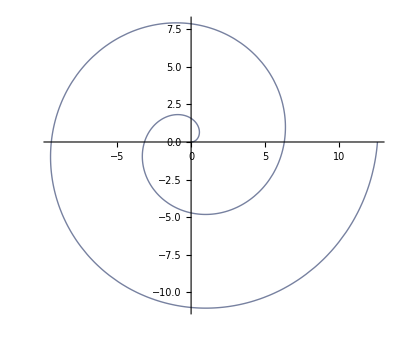

```mathematica
ParametricPlot[{u Cos[u],u Sin[u]},{u,0,4 Pi},
ColorFunction->Function[{x,y,u},Hue[x+u]],PlotStyle->Thick]
```

```mathematica
Information[ParametricPlot]
```

```mathematica
Graphics3D[Sphere[{0,0,0},1]]
```

-Graphics3D-

```mathematica
SampleSize=1234;
Dots=Graphics3D[{Sphere[{0,0,0},0.99],PointSize[0.02],Table[
x=Normalize[RandomReal[{-1,1},m]];
{Hue[0.9(x.A.x-λMin)/(λMax-λMin)],Point[x]},
{SampleSize}]}]
```

-Graphics3D-

```mathematica
TabView[{
Show[Dots,ViewPoint->3V⟦1⟧],
Show[Dots,ViewPoint->3V⟦2⟧],
Show[Dots,ViewPoint->3V⟦3⟧]
}]
```

123

```mathematica
SampleSize=123;
Graphics3D[Table[
x=Normalize[RandomReal[{-1,1},m]];
{Hue[0.9(x.A.x+λAbsMax)/(2λAbsMax)],Point[x]},
{SampleSize}]]
```

-Graphics3D-

```mathematica
{λs,V}=Eigensystem[A];
Show[
ParametricPlot3D[{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},{θ,0, 2π},{ϕ,0, π},
ColorFunction->Function[{x1,x2,x3},Hue[{x1,x2,x3}.A.{x1,x2,x3}]],
PlotPoints->{50, 50}],
Graphics3D[{PointSize[0.04],Point[V],Point[-V]}]
]
```

-Graphics3D-

```mathematica
A={{2.0,1,0},
  {1,2,1},
{0,1,3}};
λs=Eigenvalues[A]
{λMin,λMax}={Min[λs],Max[λs]}
Pic=ParametricPlot3D[ {
{r Cos[θ],r Sin[θ],√(1-r^2)},
{r Cos[θ],r Sin[θ],-√(1-r^2)}
},{θ,0,2π},{r,0,1},
ColorFunctionScaling->True,
ColorFunction:>Function[{x,y,z,θ,r},Hue[0.9 ({x,y,z}.A.{x,y,z}-λMin)/(λMax-λMin)]],
PlotPoints->100
]
```

{3.80194,2.44504,0.75302}

{0.75302,3.80194}

-Graphics3D-

```mathematica
PicDown=ParametricPlot3D[ {r Cos[θ],r Sin[θ],-√(1-r^2)},{θ,0,2π},{r,0,1},
ColorFunctionScaling->True,
ColorFunction:>Function[{x,y,z,θ,r},Hue[{x,y,z}.A.{x,y,z}]],
PlotPoints->100
];
Show[PicUp,PicDown]
```

{3.80194,2.44504,0.75302}

{0.75302,3.80194}

-Graphics3D-

```mathematica
$Version
```

13.0.0 for Microsoft Windows (64-bit) (December 3, 2021)

```mathematica
Show[PicUp,PicDown]
```

-Graphics3D-

```mathematica
Show[
ParametricPlot3D[ {r Cos[θ],r Sin[θ],√(1-r^2)},{θ,0,2π},{r,0,1},
ColorFunctionScaling->True,
ColorFunction:>Function[{x,y,z,θ,r},Hue[{x,y,z}.A.{x,y,z}]],
PlotPoints->100
],
ParametricPlot3D[ {r Cos[θ],r Sin[θ],-√(1-r^2)},{θ,0,2π},{r,0,1},
ColorFunctionScaling->True,
ColorFunction:>Function[{x,y,z,θ,r},Hue[{x,y,z}.A.{x,y,z}]],
PlotPoints->100
]]
```

{3.80194,2.44504,0.75302}

{0.75302,3.80194}

-Graphics3D-

```mathematica
?MeshShading
```

```mathematica
{λs,Map[r[A,#]&, V]}ᵀ
```

{{2.54721,2.54721},{-1.18404,-1.18404},{-0.0333128,-0.0333128}}

```mathematica
m=3; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_,x_]:= x.A.x/(x.x)
{v1,v2,v3}=Eigenvectors[A];
Show[
ParametricPlot3D[{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},{θ,0, 2π},{ϕ,0, π},
ColorFunction->Function[{x1,x2,x3,θ,ϕ},Hue[r[A,{x1,x2,x3}]]],
PlotPoints->{20, 20}],
Graphics3D[{PointSize[0.04],Map[Point,{v1,-v1,v2,-v2,v3,-v3}]}]
]
```

-Graphics3D-

```mathematica
{u1,u2}=Map[Normalize,RandomReal[{-1,1},{2,3}]];
SetOptions[ContourPlot,Contours->54,PlotPoints->50,Epilog->{Red,Point[{0,0}]}];
TabView[{
1->ContourPlot[r[A][v1+ϵ1 u1 +ϵ2 u2],{ϵ1,-0.5,0.5},{ϵ2,-0.5,0.5}],
2->ContourPlot[r[A][v2+ϵ1 u1 +ϵ2 u2],{ϵ1,-0.5,0.5},{ϵ2,-0.5,0.5}],
3->ContourPlot[r[A][v3+ϵ1 u1 +ϵ2 u2],{ϵ1,-0.5,0.5},{ϵ2,-0.5,0.5}]
}]
```

123

## Backsubstitution: Function

```mathematica
BackSubstitution[R_,b_]:=Module[{x=0*R,m},
m=Length[R];
(* R is assumed to be square and lower triangular *)
Do[
x⟦j⟧=(b⟦j⟧-Sum[R⟦j,k⟧x⟦k⟧,{k,j+1,m}])/R⟦j,j⟧,
{j,m,1,-1}];
(* return x *)
x
]
```

Test.

```mathematica
m=6; 
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
b=RandomReal[{-1,1},m];
LinearSolve[R,b]
BackSubstitution[R,b]
```

{-0.808741,-16.289,-8.65091,2.60397,-1.95016,0.20795}

{-0.808741,-16.289,-8.65091,2.60397,-1.95016,0.20795}

### Bad News abut Char Polys

Whatever